```mathematica
pivot[iStar_, jStar_, tableau_] := (
newTableau = tableau;
numberRows = Dimensions[tableau][[1]];
numberCols = Dimensions[tableau][[2]];
(* switch row tableau variables *)
newTableau[[1,jStar]] = tableau[[iStar, numberCols]];
newTableau[[iStar, numberCols]] = tableau[[1,jStar]];
(* switch column tableau variables *)
newTableau[[numberRows,jStar]] = -tableau[[iStar, 1]];
newTableau[[iStar, 1]] = -tableau[[numberRows,jStar]];
(* adjust loop bounds to skip 1st column and last row *)
For[i = 2, i < numberRows, i++,
For[j=2,j<numberCols,j++,
If[i == iStar && j == jStar, 
newTableau[[i,j]]=1/tableau[[iStar, jStar]]];
If[i== iStar && j ≠ jStar,
newTableau[[i, j]]= -tableau[[iStar, j]]/tableau[[iStar, jStar]]];
If[i ≠ iStar && j == jStar,
newTableau[[i, j]]= tableau[[i, jStar]]/tableau[[iStar, jStar]]];
If[i ≠ iStar && j ≠ jStar,
newTableau[[i, j]] = tableau[[i, j]]-tableau[[iStar, j]]*tableau[[i, jStar]]/tableau[[iStar,jStar]]];
]
];
Return[newTableau];
)
```

```mathematica
(* HW 13.1 *)
```

```mathematica
m0={" ","x1","x2",1," "};
m1={"y1",-4,-8,1500,"s1"};
m2={"y2",-6,-5,1200,"s2"};
m3={"y3",-1,0,25,"s3"};
m4={"y4",0,-1,20,"s4"};
mobj={-1,-24,-28,0,-"z"};
mLast={" ",-"v1",-"v2","w"," "};
a={m0,m1,m2,mobj,mLast};
Print["initial tableau : ",MatrixForm[a]]
```

initial tableau : (  | x1 | x2 | 1 |  
y1 | -4 | -8 | 1500 | s1
y2 | -6 | -5 | 1200 | s2
-1 | -24 | -28 | 0 | -z
  | -v1 | -v2 | w |  )

```mathematica
b=pivot[3,2,a];
Print["b = ",MatrixForm[b]];
```

b = (  | s2 | x2 | 1 |  
y1 | 2/3 | -14/3 | 700 | s1
v1 | -1/6 | -5/6 | 200 | x1
-1 | 4 | -8 | -4800 | -z
  | -y2 | -v2 | w |  )

```mathematica
c=pivot[2,3,b];
Print["optimal tableau = ",MatrixForm[c]]
```

optimal tableau = (  | s2 | s1 | 1 |  
v2 | 1/7 | -3/14 | 150 | x2
v1 | -2/7 | 5/28 | 75 | x1
-1 | 20/7 | 12/7 | -6000 | -z
  | -y2 | -y1 | w |  )

```mathematica
(* 
optimal production plan: 75 forks (x1) and 150 spoons 
(x2) max revenue = $6,000
*)
```

```mathematica
(* b buy more pewter? yes because y1* =12/7 > 1=p1 = mkt on pewter *)
```

4 x1+8 x2

6 x1+5 x2

(375-x1)/2

-6/5 (-200+x1)

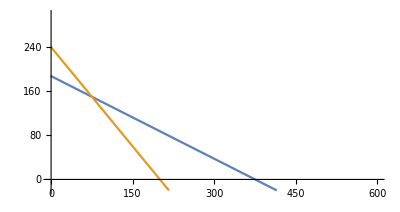

```mathematica
Clear[x1,x2]
g1[x1_,x2_]=4x1+8x2 (* ≤ 1500 *) (* pewter p1 = $1 < y1* = $12/7 so buy *)
g2[x1_,x2_]=6x1+5x2(* ≤ 1200 *)(* ebony p2 = $2 *)
g1[x1_]=x2/.Solve[g1[x1,x2]==1500,{x2}][[1,1]]
g2[x1_]=x2/.Solve[g2[x1,x2]==1200,{x2}][[1,1]]
(* optionally plot objective function to help visualize the situation. pick a level set that will show up in picture. z(200,200) = 10400 so the level set will go through (200,200) 
z[x1_,x2_]:=24x1+28x2(* objective function *)
z[x1_]:=x2/.Solve[z[x1,x2]==10400,{x2}][[1,1]]  *)

Plot[{g1[x],g2[x],z[x]},{x,-1,600},AspectRatio->Automatic,PlotRange->{-20,300}]
```

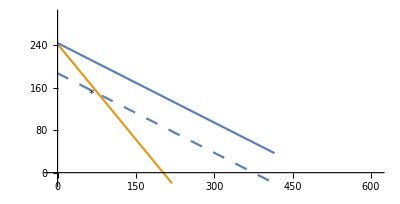

```mathematica
(* buy pewter, i.e. increase b1 to move the blue line as far as possible before it no longer touches the feasible region. *)
Solve[g2[x1,x2]==1200&&x1==0]
```

{{x1→0,x2→240}}

```mathematica
g1[0,240]
```

1920

```mathematica
(* buy 420 oz pewter *)
```

```mathematica
m0={" ","x1","x2",1," "};
m1={"y1",-4,-8,1500+420,"s1"};
m2={"y2",-6,-5,1200,"s2"};
mobj={-1,-24,-28,420,-"z"}; (* substract $420 from z for cost of pewter: z=24x1+28x2-420 *)
mLast={" ",-"v1",-"v2","w"," "};
a={m0,m1,m2,mobj,mLast};
Print["initial tableau : ",MatrixForm[a]]
```

initial tableau : (  | x1 | x2 | 1 |  
y1 | -4 | -8 | 1920 | s1
y2 | -6 | -5 | 1200 | s2
-1 | -24 | -28 | 420 | -z
  | -v1 | -v2 | w |  )

```mathematica
b=pivot[3,2,a];
Print["b = ",MatrixForm[b]];
```

b = (  | s2 | x2 | 1 |  
y1 | 2/3 | -14/3 | 1120 | s1
v1 | -1/6 | -5/6 | 200 | x1
-1 | 4 | -8 | -4380 | -z
  | -y2 | -v2 | w |  )

```mathematica
c=pivot[2,3,b];
Print["optimal tableau y* = ",MatrixForm[c]]
```

optimal tableau y* = (  | s2 | s1 | 1 |  
v2 | 1/7 | -3/14 | 240 | x2
v1 | -2/7 | 5/28 | 0 | x1
-1 | 20/7 | 12/7 | -6300 | -z
  | -y2 | -y1 | w |  )

```mathematica
(* zero in b column indicates multiple dual solutions so pivot on positive entry in the row of the zero to get another optimal tableau *)
d=pivot[3,3,c];
Print["optimal tableau y^ = ",MatrixForm[d]]
```

optimal tableau y^ = (  | s2 | x1 | 1 |  
v2 | -1/5 | -6/5 | 240 | x2
y1 | 8/5 | 28/5 | 0 | s1
-1 | 28/5 | 48/5 | -6300 | -z
  | -y2 | -v1 | w |  )

```mathematica
(* zero in b column and multiple positive entries in the row of the zero so do column tableau ratio test: set i = row of zero and choose j to minimize absolute_value(cj/aij) *)
Sort[{(28/5)/(8/5),(48/5)/(28/5)}]
```

{12/7,7/2}

```mathematica
(* x1 column wins ratio test and pivoting on x1 and s1 just goes back to y* so no more optimal tableaux *)
```

```mathematica
(* HW 13.1b did not ask for this but in class we used this as example of determining rates of change *)
(* Each following plot is for db1 or db2 positive or negative *)
```

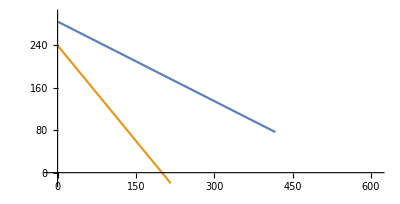

```mathematica
(* db1 =1, use y^ => dz*=0 *)
```

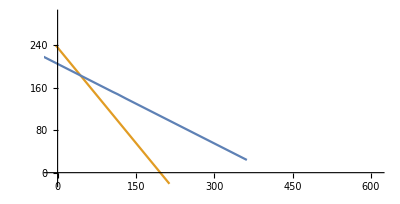

```mathematica
(* db1 = -1, use y* => dz* = -12/7 *)
```

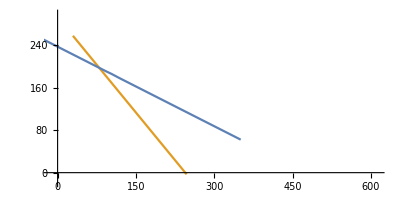

```mathematica
(* db2 = 3, use y* => dz* = y2* db2 = 20/7 3 = 60/7 (because db2 = 3 not 1) *)
```

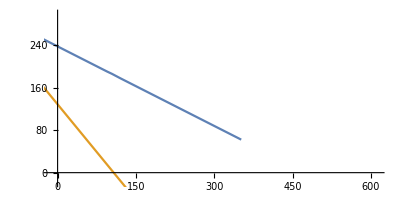

```mathematica
(* db2 = -, use y* => dz* = y2* db2 = 20/7 3 = 60/7 (because db2 = 3 not 1) *)
```

```mathematica
(* c *)
(* At original solution y2* = 20/7 > 2 = p2 = market price of ebony so it is profitable to buy more ebony *)
```

```mathematica
(*  To determine how much ebony to buy move the enbony line as far as possible before it no longer touches the feasible region.*)
```

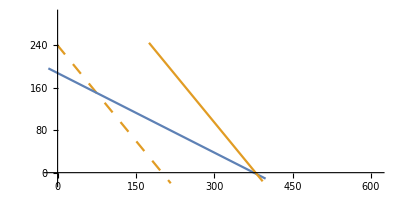

```mathematica
Solve[g1[x1,x2]==1500&&x2==0]
```

{{x1→375,x2→0}}

```mathematica
g2[375,0]
```

2250

```mathematica
(* buy 1050 oz ebony *)
```

```mathematica
m0={" ","x1","x2",1," "};
m1={"y1",-4,-8,1500,"s1"};
m2={"y2",-6,-5,1200+1050,"s2"};
mobj={-1,-24,-28,2100,-"z"}; (* substract 2100 from z for cost of ebony: z=24x1+28x2-2100 *)
mLast={" ",-"v1",-"v2","w"," "};
a={m0,m1,m2,mobj,mLast};
Print["initial tableau : ",MatrixForm[a]]
```

initial tableau : (  | x1 | x2 | 1 |  
y1 | -4 | -8 | 1500 | s1
y2 | -6 | -5 | 2250 | s2
-1 | -24 | -28 | 2100 | -z
  | -v1 | -v2 | w |  )

```mathematica
b=pivot[3,2,a];
Print["b = ",MatrixForm[b]];
```

b = (  | s2 | x2 | 1 |  
y1 | 2/3 | -14/3 | 0 | s1
v1 | -1/6 | -5/6 | 375 | x1
-1 | 4 | -8 | -6900 | -z
  | -y2 | -v2 | w |  )

```mathematica
c=pivot[2,3,b];
Print["optimal tableau y* = ",MatrixForm[c]]
```

optimal tableau y* = (  | s2 | s1 | 1 |  
v2 | 1/7 | -3/14 | 0 | x2
v1 | -2/7 | 5/28 | 375 | x1
-1 | 20/7 | 12/7 | -6900 | -z
  | -y2 | -y1 | w |  )

```mathematica
(* zero in b column indicates multiple dual solutions so pivot on positive entry in the row of the zero to get another optimal tableau *)
d=pivot[2,2,c];
Print["optimal tableau y^ = ",MatrixForm[d]]
```

optimal tableau y^ = (  | x2 | s1 | 1 |  
y2 | 7 | 3/2 | 0 | s2
v1 | -2 | -1/4 | 375 | x1
-1 | 20 | 6 | -6900 | -z
  | -v2 | -y1 | w |  )

```mathematica
(* you could do same exploration of rates of change here *)
```

```mathematica
(* d *)
```

```mathematica
(* return on investent aka roi = (yi* - pi)/pi e.g. if you invest $100 and get back $150 you profited $50 on your $100 investment so roi = 50% *)
(* if you have fixed budget then invest so as to get the best roi on your investment *)
```

```mathematica
(* y1*/p1 =(12/7)/1 > (20/7)/2 =y2*/p2 => better roi on b1=pewter than on b1=ebony *)
(* roi = profit per dollar = (dz*-d$)/d$ *)
```

```mathematica
(* if budget is small you just invest it all in the highest roi resource *)
(* if budget is big enough that dual solution changes before you run out of money then you can get into a lot of back and forth buy pewter until y1* becomes zero then buy ebony but as soon as buy any ebony you can immediately buy a little more pewter and so on *)
```

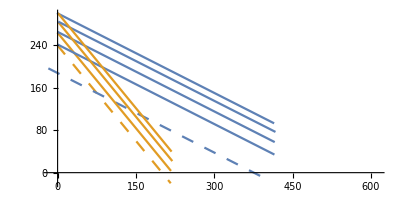

```mathematica
(* The amounts of pewter and ebony to buy to exactly send the budget as indicated in the above plot can be solved for by including the extra purchase of pewter and ebony in the LP *)
(* Let x3 = extra pewter purchased and x4 = extra ebony purchased and new LP becomes 
max 24x1+28x2-x3-2x4
4x1+8x2-x3+0x4≤1500
6x1+5x2+0x3-x4≤1200
0x1+0x2+1x3+2x4≤1000
x≥0
*)
```

```mathematica
m0={" ","x1","x2","x3","x4",1," "};
m1={"y1",-4,-8,1,0,1500.,"s1"};
m2={"y2",-6,-5,0,1,1200.,"s2"};
m3={"y3",0,0,-1,-2,1000.,"s3"};
mobj={-1,-24,-28,1,2,0.,-"z"};
mLast={" ",-"v1",-"v2",-"v3",-"v4","w"," "};
a={m0,m1,m2,m3,mobj,mLast};
Print["initial tableau : ",MatrixForm[a]]
```

initial tableau : (  | x1 | x2 | x3 | x4 | 1 |  
y1 | -4 | -8 | 1 | 0 | 1500. | s1
y2 | -6 | -5 | 0 | 1 | 1200. | s2
y3 | 0 | 0 | -1 | -2 | 1000. | s3
-1 | -24 | -28 | 1 | 2 | 0. | -z
  | -v1 | -v2 | -v3 | -v4 | w |  )

```mathematica
Sort[{1500/4,1200/6}]
```

{200,375}

```mathematica
b=pivot[3,2,a];
Print["b = ",MatrixForm[b]];
```

b = (  | s2 | x2 | x3 | x4 | 1 |  
y1 | 2/3 | -14/3 | 1 | -2/3 | 700. | s1
v1 | -1/6 | -5/6 | 0 | 1/6 | 200. | x1
y3 | 0 | 0 | -1 | -2 | 1000. | s3
-1 | 4 | -8 | 1 | -2 | -4800. | -z
  | -y2 | -v2 | -v3 | -v4 | w |  )

```mathematica
Sort[{700/(14/3),200/(5/6)}]
Ordering[{700/(14/3),200/(5/6)}]
```

{150,240}

{1,2}

```mathematica
c=pivot[2,3,b];
Print["optimal tableau = ",MatrixForm[c]]
```

optimal tableau = (  | s2 | s1 | x3 | x4 | 1 |  
v2 | 1/7 | -3/14 | 3/14 | -1/7 | 150. | x2
v1 | -2/7 | 5/28 | -5/28 | 2/7 | 75. | x1
y3 | 0 | 0 | -1 | -2 | 1000. | s3
-1 | 20/7 | 12/7 | -5/7 | -6/7 | -6000. | -z
  | -y2 | -y1 | -v3 | -v4 | w |  )

```mathematica
(* notice this tableau represents the original solution before more resources are purchased and pivoting down x3 and x4 represents buying pewter and ebony *)
```

```mathematica
Sort[{75/(5/28),1000/1}]
```

{420,1000}

```mathematica
d=pivot[3,4,c];
Print["optimal tableau = ",MatrixForm[d]]
```

optimal tableau = (  | s2 | s1 | x1 | x4 | 1 |  
v2 | -1/5 | 0 | -6/5 | 1/5 | 240. | x2
v3 | -8/5 | 1 | -28/5 | 8/5 | 420. | x3
y3 | 8/5 | -1 | 28/5 | -18/5 | 580. | s3
-1 | 4 | 1 | 4 | -2 | -6300. | -z
  | -y2 | -y1 | -v1 | -v4 | w |  )

```mathematica
(* notice pivoting down x3 results in a purchase of 420 ounces of pewter which is the same solution found in b *)
```

```mathematica
e=pivot[4,5,d];
Print["optimal tableau = ",MatrixForm[e]]
```

optimal tableau = (  | s2 | s1 | x1 | s3 | 1 |  
v2 | -1/9 | -1/18 | -8/9 | -1/18 | 272.222 | x2
v3 | -8/9 | 5/9 | -28/9 | -4/9 | 677.778 | x3
v4 | 4/9 | -5/18 | 14/9 | -5/18 | 161.111 | x4
-1 | 28/9 | 14/9 | 8/9 | 5/9 | -6622.22 | -z
  | -y2 | -y1 | -v1 | -y3 | w |  )

```mathematica
(* Spending the full $1000 budget with x1 = 0 results in 677.778 ounces of pewter at $1/ounce and 161.111 ounces of ebony at $2/ounce *)
```

```mathematica
(* e *)
(* There was no "e" in HW 13.1 but in offcie hours the question arose about borrowing money to increase the investment budget *)
(* With $1000 budget y3* = 5/9 = ROI on investment dollars so it is profitable to borrow funds to purchase resources as long as the interest rate is less than 5/9 *)
(* Set interest rate = 1/4 and set credit limit at $10000 *)
(* new LP with variable investment budget=$1000+x5 where x5 is money borrowed at 25% 
max 24x1+28x2-x3-2x4-x5/4
4x1+8x2-x3+0x4+0x5≤1500
6x1+5x2+0x3-x4+0x5≤1200
0x1+0x2+1x3+2x4-x5≤1000
0x1+0x2+0x3+0x4+x5≤10000
x≥0
*)
```

```mathematica
m0={" ","x1","x2","x3","x4","x5",1," "};
m1={"y1",-4,-8,1,0,0,1500.,"s1"};
m2={"y2",-6,-5,0,1,0,1200.,"s2"};
m3={"y3",0,0,-1,-2,1,1000.,"s3"};
m4={"y4",0,0,0,0,-1,10000.,"s4"};
mobj={-1,-24,-28,1,2,1/4,0.,-"z"};
mLast={" ",-"v1",-"v2",-"v3",-"v4",-"v5","w"," "};
a={m0,m1,m2,m3,m4,mobj,mLast};
Print["initial tableau : ",MatrixForm[a]]
```

initial tableau : (  | x1 | x2 | x3 | x4 | x5 | 1 |  
y1 | -4 | -8 | 1 | 0 | 0 | 1500. | s1
y2 | -6 | -5 | 0 | 1 | 0 | 1200. | s2
y3 | 0 | 0 | -1 | -2 | 1 | 1000. | s3
y4 | 0 | 0 | 0 | 0 | -1 | 10000. | s4
-1 | -24 | -28 | 1 | 2 | 1/4 | 0. | -z
  | -v1 | -v2 | -v3 | -v4 | -v5 | w |  )

```mathematica
Sort[{1500/4,1200/6}]
```

{200,375}

```mathematica
b=pivot[3,2,a];
Print["b = ",MatrixForm[b]];
```

b = (  | s2 | x2 | x3 | x4 | x5 | 1 |  
y1 | 2/3 | -14/3 | 1 | -2/3 | 0 | 700. | s1
v1 | -1/6 | -5/6 | 0 | 1/6 | 0 | 200. | x1
y3 | 0 | 0 | -1 | -2 | 1 | 1000. | s3
y4 | 0 | 0 | 0 | 0 | -1 | 10000. | s4
-1 | 4 | -8 | 1 | -2 | 1/4 | -4800. | -z
  | -y2 | -v2 | -v3 | -v4 | -v5 | w |  )

```mathematica
Sort[{700/(14/3),200/(5/6)}]
Ordering[{700/(14/3),200/(5/6)}]
```

{150,240}

{1,2}

```mathematica
c=pivot[2,3,b];
Print["optimal tableau = ",MatrixForm[c]]
```

optimal tableau = (  | s2 | s1 | x3 | x4 | x5 | 1 |  
v2 | 1/7 | -3/14 | 3/14 | -1/7 | 0 | 150. | x2
v1 | -2/7 | 5/28 | -5/28 | 2/7 | 0 | 75. | x1
y3 | 0 | 0 | -1 | -2 | 1 | 1000. | s3
y4 | 0 | 0 | 0 | 0 | -1 | 10000. | s4
-1 | 20/7 | 12/7 | -5/7 | -6/7 | 1/4 | -6000. | -z
  | -y2 | -y1 | -v3 | -v4 | -v5 | w |  )

```mathematica
Sort[{75/(5/28),1000/1}]
```

{420,1000}

```mathematica
d=pivot[3,4,c];
Print["optimal tableau = ",MatrixForm[d]]
```

optimal tableau = (  | s2 | s1 | x1 | x4 | x5 | 1 |  
v2 | -1/5 | 0 | -6/5 | 1/5 | 0 | 240. | x2
v3 | -8/5 | 1 | -28/5 | 8/5 | 0 | 420. | x3
y3 | 8/5 | -1 | 28/5 | -18/5 | 1 | 580. | s3
y4 | 0 | 0 | 0 | 0 | -1 | 10000. | s4
-1 | 4 | 1 | 4 | -2 | 1/4 | -6300. | -z
  | -y2 | -y1 | -v1 | -v4 | -v5 | w |  )

```mathematica
e=pivot[4,5,d];
Print["e = ",MatrixForm[e]]
```

optimal tableau = (  | s2 | s1 | x1 | s3 | x5 | 1 |  
v2 | -1/9 | -1/18 | -8/9 | -1/18 | 1/18 | 272.222 | x2
v3 | -8/9 | 5/9 | -28/9 | -4/9 | 4/9 | 677.778 | x3
v4 | 4/9 | -5/18 | 14/9 | -5/18 | 5/18 | 161.111 | x4
y4 | 0 | 0 | 0 | 0 | -1 | 10000. | s4
-1 | 28/9 | 14/9 | 8/9 | 5/9 | -11/36 | -6622.22 | -z
  | -y2 | -y1 | -v1 | -y3 | -v5 | w |  )

```mathematica
f=pivot[5,6,e];
Print["f = ",MatrixForm[f]]
```

f = (  | s2 | s1 | x1 | s3 | s4 | 1 |  
v2 | -1/9 | -1/18 | -8/9 | -1/18 | -1/18 | 827.778 | x2
v3 | -8/9 | 5/9 | -28/9 | -4/9 | -4/9 | 5122.22 | x3
v4 | 4/9 | -5/18 | 14/9 | -5/18 | -5/18 | 2938.89 | x4
v5 | 0 | 0 | 0 | 0 | -1 | 10000. | x5
-1 | 28/9 | 14/9 | 8/9 | 5/9 | 11/36 | -9677.78 | -z
  | -y2 | -y1 | -v1 | -y3 | -y4 | w |  )

```mathematica
(* Without demand constraints it would be profitable to continue borrowing money. The marginal value of a higher credit limit is y4*=11/36=marginal value of more investment budget minus the inetrest rate you pay to get the increase in budget *)
```

```mathematica
5/9-1/4
```

11/36

```mathematica
(* f *)
(* No "f" in original problem but in office hours we discussed how demand constraints could make it not profitable to spend the entire investment budget so we re-solved with demand constraints x1≤300 and x2≤400 *)
```

```mathematica
(* new LP with resource purchase budget and ability to borrow up to $10000 at 25% and demand constraints 
max 24x1+28x2-x3-2x4-x5/4
4x1+8x2-x3+0x4+0x5≤1500
6x1+5x2+0x3-x4+0x5≤1200
0x1+0x2+1x3+2x4-x5≤1000
0x1+0x2+0x3+0x4+x5≤10000
1x1+0x2+0x3+0x4+0x5≤300
0x1+1x2+0x3+0x4+0x5≤400
x≥0
*)
```

```mathematica
m0={" ","x1","x2","x3","x4","x5",1," "};
m1={"y1",-4,-8,1,0,0,1500.,"s1"};
m2={"y2",-6,-5,0,1,0,1200.,"s2"};
m3={"y3",0,0,-1,-2,1,1000.,"s3"};
m4={"y4",0,0,0,0,-1,10000.,"s4"};
m5={"y5",-1,0,0,0,0,300.,"s5"};
m6={"y6",0,-1,0,0,0,400.,"s6"};
mobj={-1,-24,-28,1,2,1/4,0.,-"z"};
mLast={" ",-"v1",-"v2",-"v3",-"v4",-"v5","w"," "};
a={m0,m1,m2,m3,m4,m5,m6,mobj,mLast};
Print["initial tableau : ",MatrixForm[a]]
```

initial tableau : (  | x1 | x2 | x3 | x4 | x5 | 1 |  
y1 | -4 | -8 | 1 | 0 | 0 | 1500. | s1
y2 | -6 | -5 | 0 | 1 | 0 | 1200. | s2
y3 | 0 | 0 | -1 | -2 | 1 | 1000. | s3
y4 | 0 | 0 | 0 | 0 | -1 | 10000. | s4
y5 | -1 | 0 | 0 | 0 | 0 | 300. | s5
y6 | 0 | -1 | 0 | 0 | 0 | 400. | s6
-1 | -24 | -28 | 1 | 2 | 1/4 | 0. | -z
  | -v1 | -v2 | -v3 | -v4 | -v5 | w |  )

```mathematica
Sort[{1500/4,1200/6}]
```

{200,375}

```mathematica
b=pivot[3,2,a];
Print["b = ",MatrixForm[b]];
```

b = (  | s2 | x2 | x3 | x4 | x5 | 1 |  
y1 | 2/3 | -14/3 | 1 | -2/3 | 0 | 700. | s1
v1 | -1/6 | -5/6 | 0 | 1/6 | 0 | 200. | x1
y3 | 0 | 0 | -1 | -2 | 1 | 1000. | s3
y4 | 0 | 0 | 0 | 0 | -1 | 10000. | s4
y5 | 1/6 | 5/6 | 0 | -1/6 | 0 | 100. | s5
y6 | 0 | -1 | 0 | 0 | 0 | 400. | s6
-1 | 4 | -8 | 1 | -2 | 1/4 | -4800. | -z
  | -y2 | -v2 | -v3 | -v4 | -v5 | w |  )

```mathematica
Sort[{700/(14/3),200/(5/6)}]
Ordering[{700/(14/3),200/(5/6)}]
```

{150,240}

{1,2}

```mathematica
c=pivot[2,3,b];
Print["optimal tableau = ",MatrixForm[c]]
```

optimal tableau = (  | s2 | s1 | x3 | x4 | x5 | 1 |  
v2 | 1/7 | -3/14 | 3/14 | -1/7 | 0 | 150. | x2
v1 | -2/7 | 5/28 | -5/28 | 2/7 | 0 | 75. | x1
y3 | 0 | 0 | -1 | -2 | 1 | 1000. | s3
y4 | 0 | 0 | 0 | 0 | -1 | 10000. | s4
y5 | 2/7 | -5/28 | 5/28 | -2/7 | 0 | 225. | s5
y6 | -1/7 | 3/14 | -3/14 | 1/7 | 0 | 250. | s6
-1 | 20/7 | 12/7 | -5/7 | -6/7 | 1/4 | -6000. | -z
  | -y2 | -y1 | -v3 | -v4 | -v5 | w |  )

```mathematica
Sort[{75/(5/28),1000/1}]
```

{420,1000}

```mathematica
d=pivot[3,4,c];
Print["optimal tableau = ",MatrixForm[d]]
```

optimal tableau = (  | s2 | s1 | x1 | x4 | x5 | 1 |  
v2 | -1/5 | 0 | -6/5 | 1/5 | 0 | 240. | x2
v3 | -8/5 | 1 | -28/5 | 8/5 | 0 | 420. | x3
y3 | 8/5 | -1 | 28/5 | -18/5 | 1 | 580. | s3
y4 | 0 | 0 | 0 | 0 | -1 | 10000. | s4
y5 | 0 | 0 | -1 | 0 | 0 | 300. | s5
y6 | 1/5 | 0 | 6/5 | -1/5 | 0 | 160. | s6
-1 | 4 | 1 | 4 | -2 | 1/4 | -6300. | -z
  | -y2 | -y1 | -v1 | -v4 | -v5 | w |  )

```mathematica
e=pivot[4,5,d];
Print["e = ",MatrixForm[e]]
```

e = (  | s2 | s1 | x1 | s3 | x5 | 1 |  
v2 | -1/9 | -1/18 | -8/9 | -1/18 | 1/18 | 272.222 | x2
v3 | -8/9 | 5/9 | -28/9 | -4/9 | 4/9 | 677.778 | x3
v4 | 4/9 | -5/18 | 14/9 | -5/18 | 5/18 | 161.111 | x4
y4 | 0 | 0 | 0 | 0 | -1 | 10000. | s4
y5 | 0 | 0 | -1 | 0 | 0 | 300. | s5
y6 | 1/9 | 1/18 | 8/9 | 1/18 | -1/18 | 127.778 | s6
-1 | 28/9 | 14/9 | 8/9 | 5/9 | -11/36 | -6622.22 | -z
  | -y2 | -y1 | -v1 | -y3 | -v5 | w |  )

```mathematica
f=pivot[7,6,e];
Print["f = ",MatrixForm[f]]
```

f = (  | s2 | s1 | x1 | s3 | s6 | 1 |  
v2 | 0 | 0 | 0 | 0 | -1 | 400. | x2
v3 | 0 | 1 | 4 | 0 | -8 | 1700. | x3
v4 | 1 | 0 | 6 | 0 | -5 | 800. | x4
y4 | -2 | -1 | -16 | -1 | 18 | 7700. | s4
y5 | 0 | 0 | -1 | 0 | 0 | 300. | s5
v5 | 2 | 1 | 16 | 1 | -18 | 2300. | x5
-1 | 5/2 | 5/4 | -4 | 1/4 | 11/2 | -7325. | -z
  | -y2 | -y1 | -v1 | -y3 | -y6 | w |  )

```mathematica
Sort[{7700/16,300}]
```

{300,1925/4}

```mathematica
g=pivot[6,4,f];
Print["g = ",MatrixForm[g]]
```

g = (  | s2 | s1 | s5 | s3 | s6 | 1 |  
v2 | 0 | 0 | 0 | 0 | -1 | 400. | x2
v3 | 0 | 1 | -4 | 0 | -8 | 2900. | x3
v4 | 1 | 0 | -6 | 0 | -5 | 2600. | x4
y4 | -2 | -1 | 16 | -1 | 18 | 2900. | s4
v1 | 0 | 0 | -1 | 0 | 0 | 300. | x1
v5 | 2 | 1 | -16 | 1 | -18 | 7100. | x5
-1 | 5/2 | 5/4 | 4 | 1/4 | 11/2 | -8525. | -z
  | -y2 | -y1 | -y5 | -y3 | -y6 | w |  )

```mathematica
(* Solution is to borrow $7100 and meet demand by producing 300 units of x1 and 400 units of x2, made possible by purchasing 2900 ounces of pewter and 2600 of ebony. *)
```

```mathematica
(* The only constraint that is not active in the solution is the credit limit of $10000 because only $7100 is borrowed so s4 is 2900. The full budget is spent so s3=0. There are no unused resources so s1=s2=0 and demand is met so s5=s6=0
```